## RunSim-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Tue 13 Jun 2017 19:05:51
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Tue 13 Jun 2017 19:05:55
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

## Define a cellular template to run the model on.

4 cells

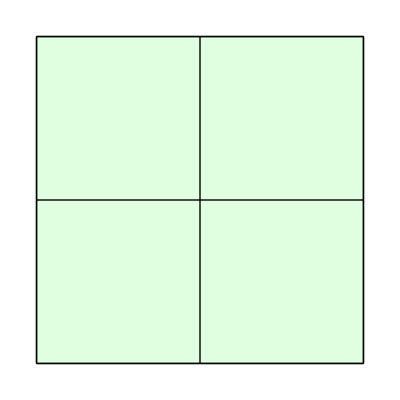

```mathematica
w=TemplateRectangularCover[10, 10, 10, 10, 0]; 
Print[n=NTissueCells[w]," cells"];
ShowTissue[w,"BoundaryStyle"->Black,"CellNumbers"->False]
```

## Define a network and illustrate how it works in a single compartment

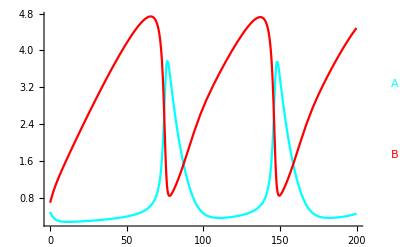

```mathematica
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
s=run[net/.parameters, timeSpan-> 200, initialConditions-> {A-> .5, B-> .7}];
runPlot[s]
```

## Generate copies of the network in all cells, including diffusion between cells, and run a simulation

```mathematica
ic[i_]:={A[i]->RandomReal[{0,.25}],B[i]->RandomReal[{0,5}]};
myic=Flatten[ic/@Range[n]];
```

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net,"Diffusion"-> {{A, DA}, {B,DB}}];
```

4 Cells.

4 internal reactions in each cell.

16 intracellular reactions.

16 diffusion reactions.

32 total reactions.

Rune a simulation using xlr8r

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,1000}]
```

{A[1]→InterpolatingFunction[{{0., 1000.}}, <>],A[2]→InterpolatingFunction[{{0., 1000.}}, <>],A[3]→InterpolatingFunction[{{0., 1000.}}, <>],A[4]→InterpolatingFunction[{{0., 1000.}}, <>],B[1]→InterpolatingFunction[{{0., 1000.}}, <>],B[2]→InterpolatingFunction[{{0., 1000.}}, <>],B[3]→InterpolatingFunction[{{0., 1000.}}, <>],B[4]→InterpolatingFunction[{{0., 1000.}}, <>]}

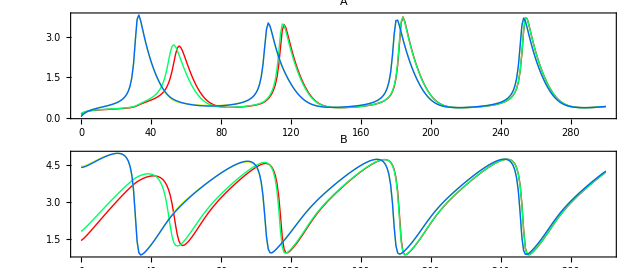

```mathematica
s=SimPlot[sim,{A, B},{0,300}, AspectRatio->.2,ImageSize->600,"Points"->300];
GraphicsColumn[s]
```